# Practical 5

# Solution of System of ordinary differential equation

A two dimensional linear system is a system of the form  
		dx/dt = ax + by
		dy/dt = c x + d y
		
		where a, b, c, d are parameters . This system can be written in matrix form as X = AX , where   
		A = (a | b
c | d)  and  X  = (x
y).
		The solutions of X = A X can be visualized as trajectories moving on the  x- y plane called the phase plane.

Example: Solve the following system of equations.
	dx/dt= - 3 x - y
	
	dy/dt = -x - 3 y

```mathematica
eq1 ={x'[t] == -3 * x[t] - y[t], y'[t]== -3 y[t] - x[t]}
```

{x'[t]==-3 x[t]-y[t],y'[t]==-x[t]-3 y[t]}

```mathematica
sol=  DSolve[eq1, {y[t],x[t]},t]
```

{{x[t]→1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)) C[1]-1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t)) C[2],y[t]→-1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t)) C[1]+1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)) C[2]}}

```mathematica
tabx = Table[x[t]/.sol[[1,1]]/. {C[1] -> i, C[2] -> j}, {i,-1,0}, {j,0,1}]//Flatten
```

{-1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)),-1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t))-1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)),0,-1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t))}

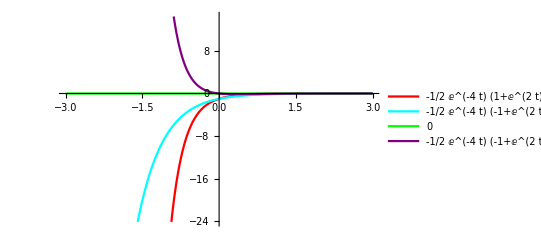

```mathematica
Plot[Evaluate[tabx], {t,-3,3}, PlotStyle-> {Red, Cyan, Green,Purple }, PlotLegends-> "Expressions"]
```

```mathematica
taby = Table[y[t]/.sol[[1,2]]/. {C[1] -> i, C[2] -> j}, {i,-1,0}, {j,0,1}]//Flatten
```

{1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t)),1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t))+1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)),0,1/2 ⅇ^(-4 t) (1+ⅇ^(2 t))}

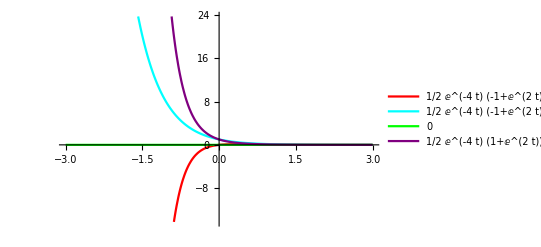

```mathematica
Plot[Evaluate[taby], {t,-3,3}, PlotStyle-> {Red, Cyan, Green,Purple }, PlotLegends-> "Expressions"]
```

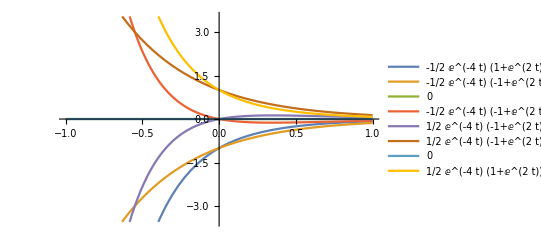

```mathematica
Plot[Evaluate[{tabx,taby}], {t,-1,1},  PlotLegends-> "Expressions"]
```

Example : Solve the following system of equations :
dx/dt= y
dy/dt= 6 x - y
with initial condition x 0 = 1, y 0 = -2

```mathematica
eq2 = {{x'[t] == y[t],y'[t] == 6 x[t]- y[t]} ,x[0] == 1,y[0] == -2}
```

{{x'[t]==y[t],y'[t]==6 x[t]-y[t]},x[0]==1,y[0]==-2}

```mathematica
DSolve[eq2, {x[t],y[t]},t]
```

{{x[t]→1/5 ⅇ^(-3 t) (4+ⅇ^(5 t)),y[t]→2/5 ⅇ^(-3 t) (-6+ⅇ^(5 t))}}

```mathematica
{xsol[t_],ysol[t_]} = ExpandAll[{x[t],y[t]}/. Flatten[DSolve[eq2,{x[t],y[t]},t]]]
```

{(4 ⅇ^(-3 t))/5+ⅇ^(2 t)/5,-12/5 ⅇ^(-3 t)+(2 ⅇ^(2 t))/5}

```mathematica
xsol[t]
```

(4 ⅇ^(-3 t))/5+ⅇ^(2 t)/5

```mathematica
ysol[t]
```

-12/5 ⅇ^(-3 t)+(2 ⅇ^(2 t))/5

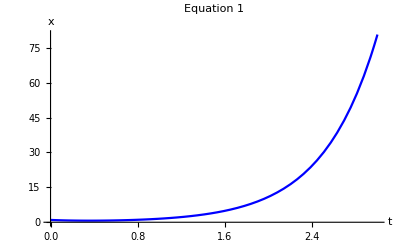

```mathematica
plot2 = Plot[xsol[t],{t,0,3}, AxesLabel-> {"t","x"},PlotLabel->" Equation 1", PlotStyle->Blue]
```

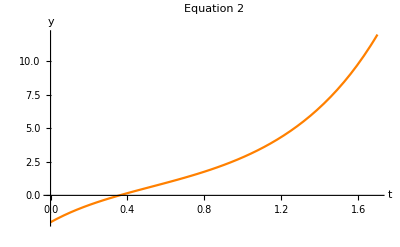

```mathematica
plot2 = Plot[ysol[t],{t,0,1.7}, AxesLabel-> {"t","y"},PlotLabel->" Equation 2", PlotStyle->Orange]
```

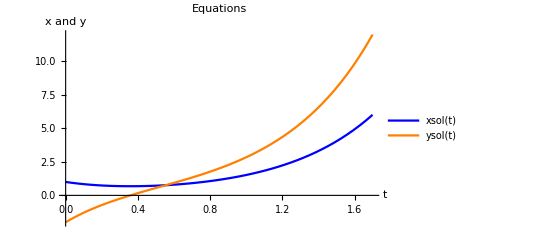

```mathematica
Plot[{xsol[t],ysol[t]},{t,0,1.7}, AxesLabel-> {"t","x and y"},PlotLabel->" Equations", PlotStyle->{Blue,Orange}, PlotLegends->"Expressions"]
```

## Unsolved Simultaneous differential equations and plot solutions:

1. dx/dt = 5 x - 2 y
	dy/dt= 4 x - y

```mathematica
ueq1 ={x'[t] == 5* x[t] - 2 y[t], y'[t]== -y[t] +4 x[t]}
```

{x'[t]==5 x[t]-2 y[t],y'[t]==4 x[t]-y[t]}

```mathematica
sol = DSolve[ueq1,{y[t],x[t]},t]
```

{{x[t]→ⅇ^t (-1+2 ⅇ^(2 t)) C[1]-ⅇ^t (-1+ⅇ^(2 t)) C[2],y[t]→2 ⅇ^t (-1+ⅇ^(2 t)) C[1]-ⅇ^t (-2+ⅇ^(2 t)) C[2]}}

```mathematica
tabx = Table[x[t]/.sol[[1,1]]/. {C[1] -> i, C[2] -> j}, {i,-1,1}, {j,0,1}]//Flatten
```

{-ⅇ^t (-1+2 ⅇ^(2 t)),-ⅇ^t (-1+ⅇ^(2 t))-ⅇ^t (-1+2 ⅇ^(2 t)),0,-ⅇ^t (-1+ⅇ^(2 t)),ⅇ^t (-1+2 ⅇ^(2 t)),-ⅇ^t (-1+ⅇ^(2 t))+ⅇ^t (-1+2 ⅇ^(2 t))}

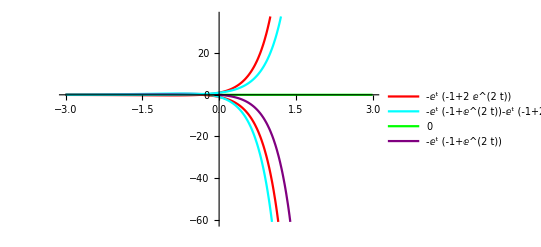

```mathematica
Plot[Evaluate[tabx], {t,-3,3}, PlotStyle-> {Red, Cyan, Green,Purple }, PlotLegends-> "Expressions"]
```

```mathematica
taby = Table[y[t]/.sol[[1,2]]/. {C[1] -> i, C[2] -> j}, {i,-1,1}, {j,0,1}]//Flatten
```

{-2 ⅇ^t (-1+ⅇ^(2 t)),-ⅇ^t (-2+ⅇ^(2 t))-2 ⅇ^t (-1+ⅇ^(2 t)),0,-ⅇ^t (-2+ⅇ^(2 t)),2 ⅇ^t (-1+ⅇ^(2 t)),-ⅇ^t (-2+ⅇ^(2 t))+2 ⅇ^t (-1+ⅇ^(2 t))}

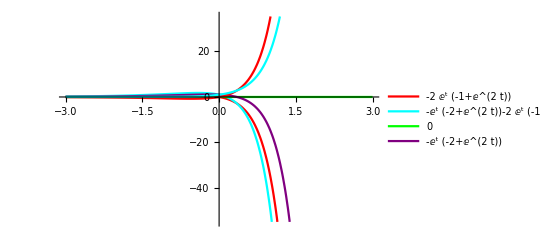

```mathematica
Plot[Evaluate[taby], {t,-3,3}, PlotStyle-> {Red, Cyan, Green,Purple }, PlotLegends-> "Expressions"]
```

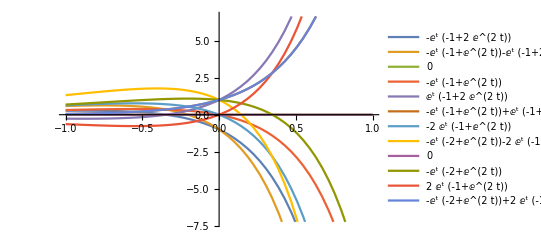

```mathematica
Plot[Evaluate[{tabx,taby}], {t,-1,1},  PlotLegends-> "Expressions"]
```

2. dx/dt= 3 x - 4 y
	dy/dt= 2 x - y

```mathematica
ueq2 ={x'[t] == 3* x[t] - 4 y[t], y'[t]== -y[t] +2 x[t]}
```

{x'[t]==3 x[t]-4 y[t],y'[t]==2 x[t]-y[t]}

```mathematica
sol2 = DSolve[ueq2,{y[t],x[t]},t]
```

{{x[t]→-2 ⅇ^t C[2] Sin[2 t]+ⅇ^t C[1] (Cos[2 t]+Sin[2 t]),y[t]→ⅇ^t C[2] (Cos[2 t]-Sin[2 t])+ⅇ^t C[1] Sin[2 t]}}

```mathematica
tabx = Table[x[t]/.sol2[[1,1]]/. {C[1] -> i, C[2] -> j}, {i,-1,1}, {j,0,1}]//Flatten
```

{-ⅇ^t (Cos[2 t]+Sin[2 t]),-2 ⅇ^t Sin[2 t]-ⅇ^t (Cos[2 t]+Sin[2 t]),0,-2 ⅇ^t Sin[2 t],ⅇ^t (Cos[2 t]+Sin[2 t]),-2 ⅇ^t Sin[2 t]+ⅇ^t (Cos[2 t]+Sin[2 t])}

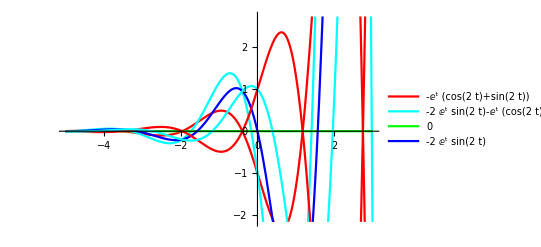

```mathematica
Plot[Evaluate[tabx], {t,-5,3}, PlotStyle-> {Red, Cyan, Green,Blue }, PlotLegends-> "Expressions"]
```

```mathematica
taby = Table[y[t]/.sol2[[1,2]]/. {C[1] -> i, C[2] -> j}, {i,-1,1}, {j,0,1}]//Flatten
```

{-ⅇ^t Sin[2 t],ⅇ^t (Cos[2 t]-Sin[2 t])-ⅇ^t Sin[2 t],0,ⅇ^t (Cos[2 t]-Sin[2 t]),ⅇ^t Sin[2 t],ⅇ^t (Cos[2 t]-Sin[2 t])+ⅇ^t Sin[2 t]}

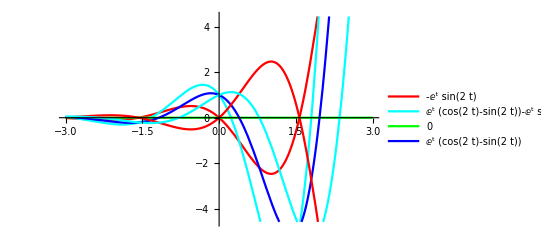

```mathematica
Plot[Evaluate[taby], {t,-3,3}, PlotStyle-> {Red, Cyan, Green,Blue }, PlotLegends-> "Expressions"]
```

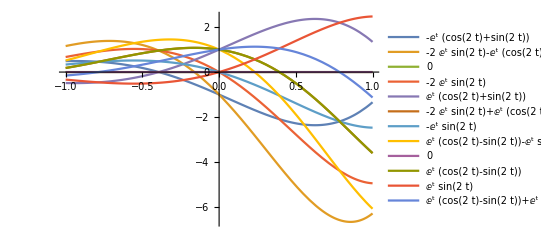

```mathematica
Plot[Evaluate[{tabx,taby}], {t,-1,1},  PlotLegends-> "Expressions"]
```

3. dx/dt= -2 x + 7 y
	dy/dt = 3 x + 2 y
 with x(0)=9,y(0)=-1

```mathematica
ueq3 ={{x'[t] == -2* x[t] + 7 y[t], y'[t]== 2 y[t] +3 x[t]}, x[0] == 9,y[0] == -1}
```

{{x'[t]==-2 x[t]+7 y[t],y'[t]==3 x[t]+2 y[t]},x[0]==9,y[0]==-1}

```mathematica
DSolve[ueq3,{y[t],x[t]},t]
```

{{x[t]→ⅇ^(-5 t) (7+2 ⅇ^(10 t)),y[t]→ⅇ^(-5 t) (-3+2 ⅇ^(10 t))}}

```mathematica
{xsol[t_],ysol[t_]} = ExpandAll[{x[t],y[t]}/. Flatten[DSolve[ueq3,{x[t],y[t]},t]]]
```

{7 ⅇ^(-5 t)+2 ⅇ^(5 t),-3 ⅇ^(-5 t)+2 ⅇ^(5 t)}

```mathematica
xsol[t]
```

7 ⅇ^(-5 t)+2 ⅇ^(5 t)

```mathematica
ysol[t]
```

-3 ⅇ^(-5 t)+2 ⅇ^(5 t)

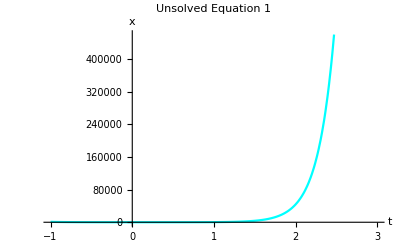

```mathematica
plot2 = Plot[xsol[t],{t,-1,3}, AxesLabel-> {"t","x"},PlotLabel->" Unsolved Equation 1", PlotStyle->Cyan]
```

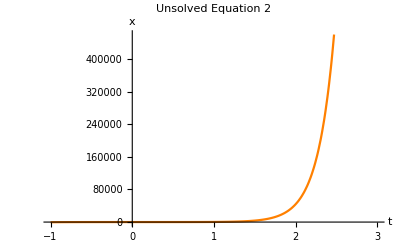

```mathematica
plot2 = Plot[ysol[t],{t,-1,3}, AxesLabel-> {"t","x"},PlotLabel->" Unsolved Equation 2", PlotStyle->Orange]
```

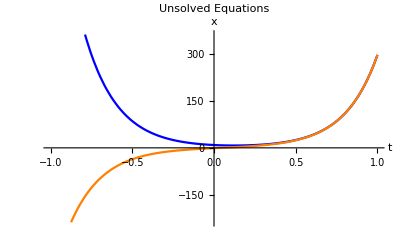

```mathematica
plot3 = Plot[{xsol[t],ysol[t]},{t,-1,1}, AxesLabel-> {"t","x"},PlotLabel->" Unsolved Equations", PlotStyle->{Blue,Orange}]
```

4.dx/dt= 7 x - y
	dy/dt= 4 x + 3 y
	with x(0)=1, y(0)=3

```mathematica
ueq4 ={{x'[t] == 7* x[t] - y[t], y'[t]== 3 y[t] +4 x[t]}, x[0] == 1,y[0] == 3}
```

{{x'[t]==7 x[t]-y[t],y'[t]==4 x[t]+3 y[t]},x[0]==1,y[0]==3}

```mathematica
DSolve[ueq4,{y[t],x[t]},t]
```

{{x[t]→-ⅇ^(5 t) (-1+t),y[t]→-ⅇ^(5 t) (-3+2 t)}}

```mathematica
{xsol[t_],ysol[t_]} = ExpandAll[{x[t],y[t]}/. Flatten[DSolve[ueq4,{x[t],y[t]},t]]]
```

{ⅇ^(5 t)-ⅇ^(5 t) t,3 ⅇ^(5 t)-2 ⅇ^(5 t) t}

```mathematica
xsol[t]
```

ⅇ^(5 t)-ⅇ^(5 t) t

```mathematica
ysol[t]
```

3 ⅇ^(5 t)-2 ⅇ^(5 t) t

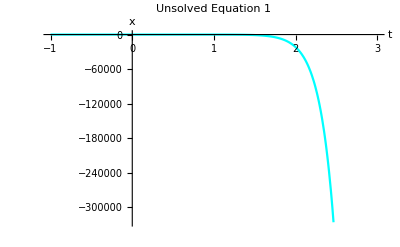

```mathematica
plot3 = Plot[xsol[t],{t,-1,3}, AxesLabel-> {"t","x"},PlotLabel->" Unsolved Equation 1", PlotStyle->Cyan]
```

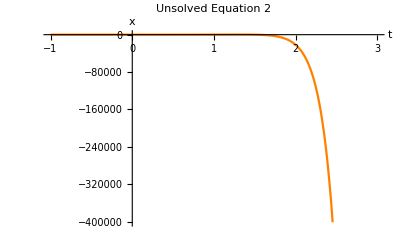

```mathematica
plot3 = Plot[ysol[t],{t,-1,3}, AxesLabel-> {"t","x"},PlotLabel->" Unsolved Equation 2", PlotStyle->Orange]
```

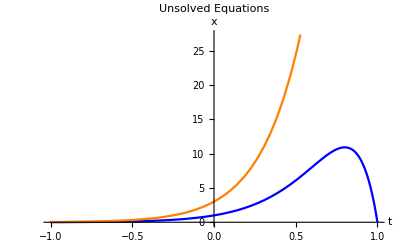

```mathematica
plot3 = Plot[{xsol[t],ysol[t]},{t,-1,1}, AxesLabel-> {"t","x"},PlotLabel->" Unsolved Equations", PlotStyle->{Blue,Orange}]
```